Q^-1/ΔE (d=1.3)
sus304
with heat flow

```mathematica
{κ->15.309,ρ->7.93 10^3,Cv->491,E0->1.99 10^11,α->16.3 10^-6}
```

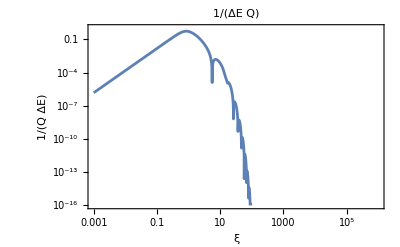

```mathematica
QHeatFlow13=Abs[3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.
{d->1.3};

QHeatFlowg=LogLogPlot[QHeatFlow13,{ξ,0.001,1000000},PlotLabel->Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

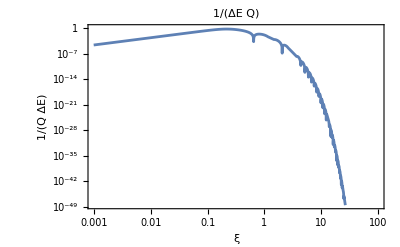

```mathematica
QHeatFlow5=Abs[3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.
{d->5};

QHeatFlowg=LogLogPlot[QHeatFlow5,{ξ,0.001,100},PlotLabel->Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

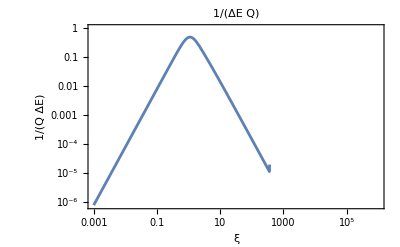

```mathematica
QHeatFlow1=Abs[3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.
{d->1};

QHeatFlow1g=LogLogPlot[QHeatFlow1,{ξ,0.001,1000000},PlotLabel->Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

without heat flow

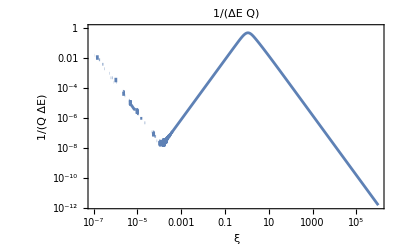

```mathematica
QNoHeatFlow =Abs[ 6/(2ξ)^2-6/(2ξ)^3(Sinh[2ξ]+Sin[2ξ])/(Cosh[2ξ]+Cos[2ξ]) ];

(*{ξ->b/2 √(ω/(2χ)),ξd->bd/2 √(ω/(2χ))}/.
{ω->2π f,χ->4.47,b->2 10^-3};*)
QNoHeatFlowg=LogLogPlot[QNoHeatFlow,{ξ,0.0000001,1000000},PlotLabel->Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

```mathematica
LogLogPlot[(x (E^x+E^-x+2)-(E^x-E^-x+2x))/(E^x+E^-x+2)6/x^3,{x,0.000001,10000}]
```

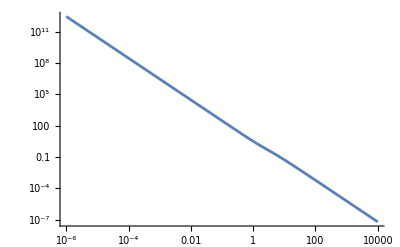

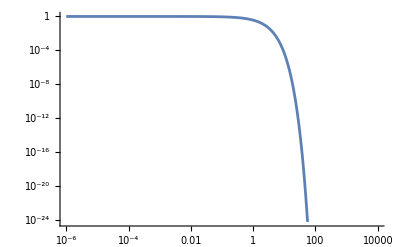

```mathematica
LogLogPlot[E^-ξ,{ξ,0.000001,10000}]
```

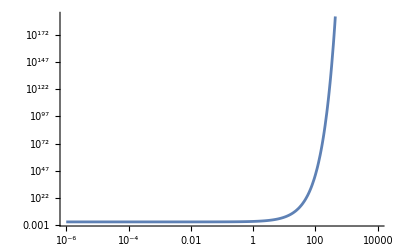

```mathematica
LogLogPlot[E^ξ,{ξ,0.000001,10000}]
```

```mathematica
FullSimplify[{Abs[3/(4 ξ^3)1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))/.{d->1}]}==Abs[6/(2ξ)^2-6/(2ξ)^3(Sinh[2ξ]+Sin[2ξ])/(Cosh[2ξ]+Cos[2ξ])]]
```

True

並べる

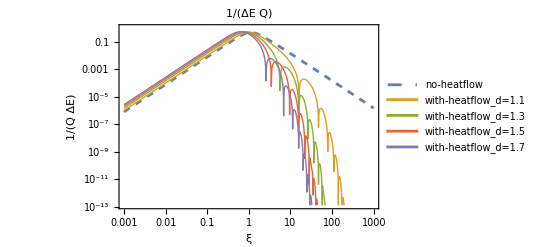

```mathematica
LogLogPlot[{QNoHeatFlow,QHeatFlow11,QHeatFlow13,QHeatFlow15,QHeatFlow17},{ξ,0.001,1000},PlotStyle->{Dashed,Thick,Thick,Thick,Thick},PlotLegends->Placed[{"no-heatflow","with-heatflow_d=1.1","with-heatflow_d=1.3","with-heatflow_d=1.5","with-heatflow_d=1.7"},{0.3,0.3}],PlotLabel->Q^-1/ΔE,Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

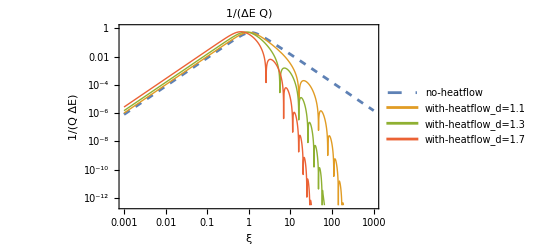

```mathematica
LogLogPlot[{QNoHeatFlow,QHeatFlow11,QHeatFlow13,QHeatFlow17},{ξ,0.001,1000},PlotStyle->{Dashed,Thick,Thick,Thick},PlotLegends->Placed[{"no-heatflow","with-heatflow_d=1.1","with-heatflow_d=1.3","with-heatflow_d=1.7"},{0.3,0.25}],PlotLabel->Q^-1/ΔE,Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```